| Estimate | Standard Error | t-Statistic | P-Value
1 | 134.23 | 3.3997 | 39.483 | 1.96459×10^-7
x | -36.6323 | 1.26364 | -28.9894 | 9.15342×10^-7

{q→134.23,Δq→3.3997}

{15.0398,6.91414}

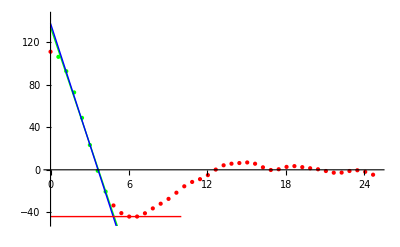

```mathematica
(*Import Data from files*)
Clear[lFit];
prefix = "PET-";
sample = "215";
path = ParentDirectory[NotebookDirectory[]] <> "/data/" <> prefix <> sample;
rawData=Import[path<>".cor","Table"];


(*Split Data into parts for linear fit and for the rest*)
sampleSize = 8;
linearData =  Take[rawData, {2,sampleSize}];
afterLinearData =  Take[rawData, -(Length[rawData ] - sampleSize)];
nonLinearData = Join[Take[rawData, 1], afterLinearData];

(*Find Min and Max of data, also find 2nd local max*)
minMax = {First@SortBy[rawData,Last], Last@SortBy[rawData,Last]};
localMax = Last@SortBy[afterLinearData,Last];

(*Linear fit*)
lFit = LinearModelFit[linearData,x,x];
lFit["ParameterTable"]


(*Relevant points*)
Δq = lFit["ParameterTable"][[1]][[1]][[2]][[3]];
q = {"q"-> lFit["Function"][0], "Δq"->Δq}
Δm = lFit["ParameterTable"][[1]][[1]][[3]][[3]];
dcP = Solve[lFit["BestFit"]+Δq-Δm*x== minMax[[1]][[2]], x][[All, 1, 2]][[1]];
dcT = {Solve[lFit["BestFit"] == minMax[[1]][[2]], x][[All, 1, 2]][[1]], minMax[[1]][[2]]};
Δdc = dcT[[1]] - dcP;
dc = {"dc"->dcT, "Δdc"->Δdc}
dac = localMax


Export[path<>"-Q-Dc-Dac-Dacy.txt", {q, dc, dac, dacy}, "Table"];
Export[path <> ".cor.txt", lFit["BestFit"], "String"];

(*Plot functions and data*)
Show[ListPlot[nonLinearData,PlotStyle->Red], ListPlot[linearData,PlotStyle->Green], Plot[{lFit["BestFit"]},{x,0,8}, PlotStyle-> Green],Plot[{lFit["BestFit"]+Δq-Δm*x},{x,0,8}, PlotStyle-> Blue], Plot[{minMax[[1]][[2]]},{x,0,10}, PlotStyle-> Red], PlotRange-> {{0,25},{minMax[[1]][[2]] - 5,lFit["Function"][0]+ 10}}]
```